```mathematica
(*Limpieza de las variables y el kernel de Mthematica*)
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
ds=Import["https://raw.githubusercontent.com/EisaacJC/COVID-19/master/DATOS%20COVID19.csv"];
```

```mathematica
key$ds=ds[[1]];
```

```mathematica
data=Dataset[Map[AssociationThread[key$ds->#]&,ds[[2;;]]]]
```

Dataset[<>]

```mathematica
fecha[dateString_: String]:=DateObject[{dateString,{"Day","Month","YearShort"}},"Day"]
```

```mathematica
data=data[All, {"Fecha"-> fecha}]
```

Dataset[<>]

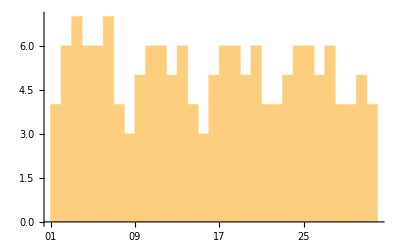

```mathematica
(*Distribución de reportes numéricos por día de mes*)data[DateHistogram[#,"Day",DateReduction->"Month"]&,"Fecha"]
```

```mathematica
key$ds
```

{Fecha,S&P/BMV IPC (MXX) CIERRE,S&P/BMV IPC (MXX) APERTURA,S&P/BMV IPC (MXX) VOL,NASDAQ CIERRRE,NASDAQ APERTURA,NASDAQ VOL,S&P 500 CIERRE,RUSELL 2000 CIERRE,RUSELL 2000 APERTURA,DOLAR CIERRE,DOLAR APERTURA,EURO CIERRE,EURO APERTURA,TITULAR MUNDIAL,UBICACIÓN,LINK MUNDIAL,Fecha ref 2,CONFIRMADOS MUNDO,CONFIRMADOS MEXICO,CONFIRMADOS USA}

```mathematica
Column[%114]
```

Column[DateListPlot[Failure[<|MessageTemplate:>Dataset::partnotapplicable,MessageParameters→<|Type→TypeSystem`Vector[TypeSystem`Struct[{Fecha,S&P/BMV IPC (MXX) CIERRE,S&P/BMV IPC (MXX) APERTURA,S&P/BMV IPC (MXX) VOL,NASDAQ CIERRRE,NASDAQ APERTURA,NASDAQ VOL,S&P 500 CIERRE,RUSELL 2000 CIERRE,RUSELL 2000 APERTURA,DOLAR CIERRE,DOLAR APERTURA,EURO CIERRE,EURO APERTURA,TITULAR MUNDIAL,UBICACIÓN,LINK MUNDIAL,Fecha ref 2,CONFIRMADOS MUNDO,CONFIRMADOS MEXICO,CONFIRMADOS USA},{TypeSystem`Atom[DateObject],TypeSystem`AnyType,TypeSystem`AnyType,TypeSystem`Atom[String],TypeSystem`AnyType,TypeSystem`AnyType,TypeSystem`Atom[String],TypeSystem`AnyType,TypeSystem`AnyType,TypeSystem`AnyType,TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[String],TypeSystem`Atom[String],TypeSystem`Atom[String],TypeSystem`Atom[String],TypeSystem`Atom[Integer],TypeSystem`Atom[Integer],TypeSystem`Atom[Integer]}],159],Part→CONFIRMADOS MEXICO,Symbol→Part|>|>,Dataset][<|Day including: Mon 2 Sep 2019 00:00:00→20.1477,Day including: Tue 3 Sep 2019 00:00:00→19.9732,Day including: Wed 4 Sep 2019 00:00:00→19.7186,Day including: Thu 5 Sep 2019 00:00:00→19.7442,Day including: Fri 6 Sep 2019 00:00:00→19.5373,Day including: Mon 9 Sep 2019 00:00:00→19.5742,Day including: Tue 10 Sep 2019 00:00:00→19.498,Day including: Wed 11 Sep 2019 00:00:00→19.509,Day including: Thu 12 Sep 2019 00:00:00→19.437,Day including: Fri 13 Sep 2019 00:00:00→19.4058,Day including: Mon 16 Sep 2019 00:00:00→19.4405,Day including: Tue 17 Sep 2019 00:00:00→19.3627,Day including: Wed 18 Sep 2019 00:00:00→19.3975,Day including: Thu 19 Sep 2019 00:00:00→19.4557,Day including: Fri 20 Sep 2019 00:00:00→19.4543,Day including: Mon 23 Sep 2019 00:00:00→19.4765,Day including: Tue 24 Sep 2019 00:00:00→19.4443,Day including: Wed 25 Sep 2019 00:00:00→19.5714,Day including: Thu 26 Sep 2019 00:00:00→19.6722,Day including: Fri 27 Sep 2019 00:00:00→19.6917,Day including: Mon 30 Sep 2019 00:00:00→19.7325,Day including: Tue 1 Oct 2019 00:00:00→19.8225,Day including: Wed 2 Oct 2019 00:00:00→19.7937,Day including: Thu 3 Oct 2019 00:00:00→19.6537,Day including: Fri 4 Oct 2019 00:00:00→19.5152,Day including: Mon 7 Oct 2019 00:00:00→19.574,Day including: Tue 8 Oct 2019 00:00:00→19.6265,Day including: Wed 9 Oct 2019 00:00:00→19.57,Day including: Thu 10 Oct 2019 00:00:00→19.4492,Day including: Fri 11 Oct 2019 00:00:00→19.3245,Day including: Mon 14 Oct 2019 00:00:00→19.2715,Day including: Tue 15 Oct 2019 00:00:00→19.2405,Day including: Wed 16 Oct 2019 00:00:00→19.202,Day including: Thu 17 Oct 2019 00:00:00→19.198,Day including: Fri 18 Oct 2019 00:00:00→19.1104,Day including: Mon 21 Oct 2019 00:00:00→19.1237,Day including: Tue 22 Oct 2019 00:00:00→19.1474,Day including: Wed 23 Oct 2019 00:00:00→19.115,Day including: Thu 24 Oct 2019 00:00:00→19.137,Day including: Fri 25 Oct 2019 00:00:00→19.0631,Day including: Mon 28 Oct 2019 00:00:00→19.12,Day including: Tue 29 Oct 2019 00:00:00→19.1225,Day including: Wed 30 Oct 2019 00:00:00→19.0811,Day including: Thu 31 Oct 2019 00:00:00→19.2345,Day including: Fri 1 Nov 2019 00:00:00→19.1117,Day including: Mon 4 Nov 2019 00:00:00→19.1735,Day including: Tue 5 Nov 2019 00:00:00→19.205,Day including: Wed 6 Nov 2019 00:00:00→19.1485,Day including: Thu 7 Nov 2019 00:00:00→19.138,Day including: Fri 8 Nov 2019 00:00:00→19.1053,Day including: Mon 11 Nov 2019 00:00:00→19.1155,Day including: Tue 12 Nov 2019 00:00:00→19.3143,Day including: Wed 13 Nov 2019 00:00:00→19.3574,Day including: Thu 14 Nov 2019 00:00:00→19.3197,Day including: Fri 15 Nov 2019 00:00:00→19.1808,Day including: Mon 18 Nov 2019 00:00:00→19.3183,Day including: Tue 19 Nov 2019 00:00:00→19.344,Day including: Wed 20 Nov 2019 00:00:00→19.466,Day including: Thu 21 Nov 2019 00:00:00→19.3858,Day including: Fri 22 Nov 2019 00:00:00→19.381,Day including: Mon 25 Nov 2019 00:00:00→19.4441,Day including: Tue 26 Nov 2019 00:00:00→19.5202,Day including: Wed 27 Nov 2019 00:00:00→19.5169,Day including: Thu 28 Nov 2019 00:00:00→19.471,Day including: Fri 29 Nov 2019 00:00:00→19.567,Day including: Mon 2 Dec 2019 00:00:00→19.5775,Day including: Tue 3 Dec 2019 00:00:00→19.5555,Day including: Wed 4 Dec 2019 00:00:00→19.433,Day including: Thu 5 Dec 2019 00:00:00→19.3765,Day including: Fri 6 Dec 2019 00:00:00→19.31,Day including: Mon 9 Dec 2019 00:00:00→19.236,Day including: Tue 10 Dec 2019 00:00:00→19.2584,Day including: Wed 11 Dec 2019 00:00:00→19.1195,Day including: Thu 12 Dec 2019 00:00:00→19.06,Day including: Fri 13 Dec 2019 00:00:00→19.0084,Day including: Mon 16 Dec 2019 00:00:00→18.9327,Day including: Tue 17 Dec 2019 00:00:00→18.935,Day including: Wed 18 Dec 2019 00:00:00→18.9675,Day including: Thu 19 Dec 2019 00:00:00→18.9205,Day including: Fri 20 Dec 2019 00:00:00→18.944,Day including: Mon 23 Dec 2019 00:00:00→18.961,Day including: Tue 24 Dec 2019 00:00:00→18.981,Day including: Wed 25 Dec 2019 00:00:00→18.979,Day including: Thu 26 Dec 2019 00:00:00→18.9405,Day including: Fri 27 Dec 2019 00:00:00→18.8394,Day including: Mon 30 Dec 2019 00:00:00→18.9315,Day including: Tue 31 Dec 2019 00:00:00→18.9325,Day including: Wed 1 Jan 2020 00:00:00→18.9325,Day including: Thu 2 Jan 2020 00:00:00→18.8395,Day including: Fri 3 Jan 2020 00:00:00→18.9245,Day including: Mon 6 Jan 2020 00:00:00→18.8445,Day including: Tue 7 Jan 2020 00:00:00→18.9055,Day including: Wed 8 Jan 2020 00:00:00→18.8155,Day including: Thu 9 Jan 2020 00:00:00→18.84,Day including: Fri 10 Jan 2020 00:00:00→18.7905,Day including: Mon 13 Jan 2020 00:00:00→18.8006,Day including: Tue 14 Jan 2020 00:00:00→18.7828,Day including: Wed 15 Jan 2020 00:00:00→18.7906,Day including: Thu 16 Jan 2020 00:00:00→18.7797,Day including: Fri 17 Jan 2020 00:00:00→18.6624,Day including: Mon 20 Jan 2020 00:00:00→18.6639,Day including: Tue 21 Jan 2020 00:00:00→18.7727,Day including: Wed 22 Jan 2020 00:00:00→18.6885,Day including: Thu 23 Jan 2020 00:00:00→18.767,Day including: Fri 24 Jan 2020 00:00:00→18.7905,Day including: Mon 27 Jan 2020 00:00:00→18.9126,Day including: Tue 28 Jan 2020 00:00:00→18.7231,Day including: Wed 29 Jan 2020 00:00:00→18.699,Day including: Thu 30 Jan 2020 00:00:00→18.7801,Day including: Fri 31 Jan 2020 00:00:00→18.8428,Day including: Mon 3 Feb 2020 00:00:00→18.8165,Day including: Tue 4 Feb 2020 00:00:00→18.667,Day including: Wed 5 Feb 2020 00:00:00→18.6005,Day including: Thu 6 Feb 2020 00:00:00→18.6603,Day including: Fri 7 Feb 2020 00:00:00→18.7683,Day including: Mon 10 Feb 2020 00:00:00→18.6977,Day including: Tue 11 Feb 2020 00:00:00→18.6594,Day including: Wed 12 Feb 2020 00:00:00→18.6198,Day including: Thu 13 Feb 2020 00:00:00→18.6,Day including: Fri 14 Feb 2020 00:00:00→18.5409,Day including: Mon 17 Feb 2020 00:00:00→18.5555,Day including: Tue 18 Feb 2020 00:00:00→18.5922,Day including: Wed 19 Feb 2020 00:00:00→18.5635,Day including: Thu 20 Feb 2020 00:00:00→18.8327,Day including: Fri 21 Feb 2020 00:00:00→18.9024,Day including: Mon 24 Feb 2020 00:00:00→19.0699,Day including: Tue 25 Feb 2020 00:00:00→19.09,Day including: Wed 26 Feb 2020 00:00:00→19.2825,Day including: Thu 27 Feb 2020 00:00:00→19.513,Day including: Fri 28 Feb 2020 00:00:00→19.6185,Day including: Mon 2 Mar 2020 00:00:00→19.405,Day including: Tue 3 Mar 2020 00:00:00→19.455,Day including: Wed 4 Mar 2020 00:00:00→19.5364,Day including: Thu 5 Mar 2020 00:00:00→19.8495,Day including: Fri 6 Mar 2020 00:00:00→20.1099,Day including: Mon 9 Mar 2020 00:00:00→20.8215,Day including: Tue 10 Mar 2020 00:00:00→20.844,Day including: Wed 11 Mar 2020 00:00:00→21.3855,Day including: Thu 12 Mar 2020 00:00:00→21.921,Day including: Fri 13 Mar 2020 00:00:00→21.9255,Day including: Mon 16 Mar 2020 00:00:00→22.885,Day including: Tue 17 Mar 2020 00:00:00→22.9594,Day including: Wed 18 Mar 2020 00:00:00→23.6665,Day including: Thu 19 Mar 2020 00:00:00→24.0275,Day including: Fri 20 Mar 2020 00:00:00→24.422,Day including: Sun 22 Mar 2020 00:00:00→24.775,Day including: Mon 23 Mar 2020 00:00:00→25.3325,Day including: Tue 24 Mar 2020 00:00:00→24.8425,Day including: Wed 25 Mar 2020 00:00:00→23.948,Day including: Thu 26 Mar 2020 00:00:00→22.943,Day including: Fri 27 Mar 2020 00:00:00→23.343,Day including: Sun 29 Mar 2020 00:00:00→23.605,Day including: Mon 30 Mar 2020 00:00:00→24.2765,Day including: Tue 31 Mar 2020 00:00:00→23.719,Day including: Wed 1 Apr 2020 00:00:00→24.24,Day including: Thu 2 Apr 2020 00:00:00→24.226,Day including: Fri 3 Apr 2020 00:00:00→25.0125,Day including: Sun 5 Apr 2020 00:00:00→25.2771,Day including: Mon 6 Apr 2020 00:00:00→24.7785|>],Joined→True,PlotMarkers→{Automatic,14},GridLines→Automatic,PlotRange→Full,ImageSize→Large]]

```mathematica
confUSA=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS USA"];
confMEX=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS MEXICO"];
```

```mathematica
confWORLD=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS MUNDO"];
```

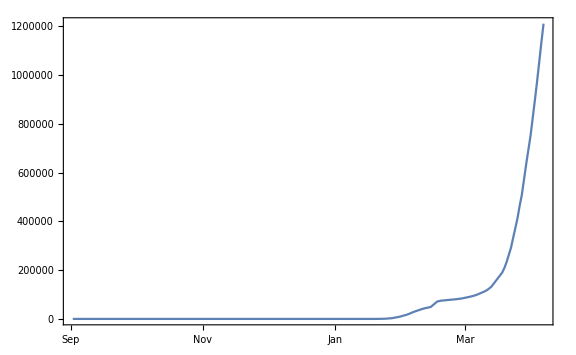

```mathematica
DateListPlot[confWORLD, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

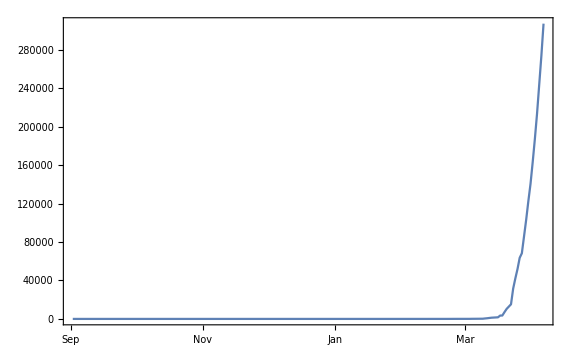

```mathematica
DateListPlot[confUSA, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

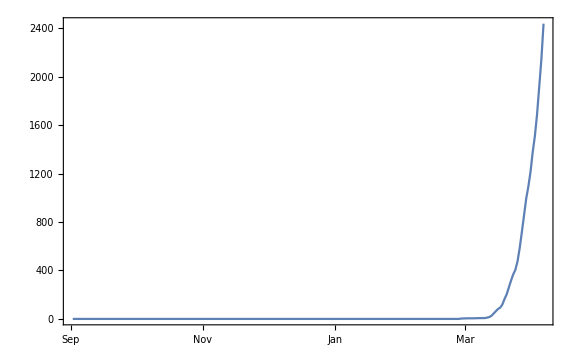

```mathematica
DateListPlot[confMEX, GridLines->Automatic,PlotRange->Full,ImageSize->Large] (*Tiene un pico el día final porque a la hora de captura de datos no se tiene registro de los nuevos casos*)
```

```mathematica
confMEXPos=GroupBy[Select[data,#["CONFIRMADOS MEXICO"]>0&],"CONFIRMADOS MEXICO"]
```

Dataset[<>]

```mathematica
dolarcierre=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "DOLAR CIERRE"];
```

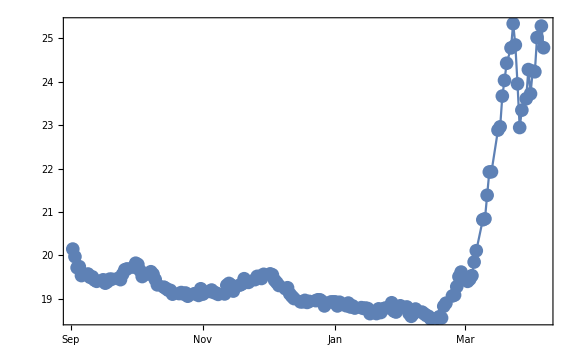

```mathematica
DateListPlot[dolarcierre,PlotMarkers->{Automatic,14}, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

```mathematica
fecha=data[GroupBy["Fecha"]]
```

Dataset[<>]

```mathematica
dolarapertura=data[GroupBy["Fecha"],Total[DeleteCases[#,""]]&,"DOLAR APERTURA"]
```

Dataset[<>]

```mathematica
SmoothHistogram[dolarcierre,PlotRange->All,PlotTheme->"Marketing"]
SmoothHistogram[dolarapertura,PlotRange->All,PlotTheme->"Marketing"]
```

-Graphics-

-Graphics-

```mathematica
dolar=data[GroupBy["Fecha"],Total[DeleteCases[#,""]]&,{"DOLAR APERTURA","DOLAR CIERRE"}]
```

Dataset[<>]

MatrixPlot::mat0: Argument Dataset[«159»] at position 1 is not a matrix.

MatrixPlot[Dataset[<>]]